{{0.0282726,0.9996},{-0.021722,0.999764},{-0.0716622,0.997429},{-0.121423,0.992601},{-0.170881,0.985292},{-0.219911,0.97552},{-0.268392,0.96331},{-0.316202,0.948692},{-0.363222,0.931703},{-0.409334,0.912385},{-0.454422,0.890786},{-0.498375,0.866961},{-0.541082,0.84097},{-0.582437,0.812876},{-0.622336,0.78275},{-0.66068,0.750668}}

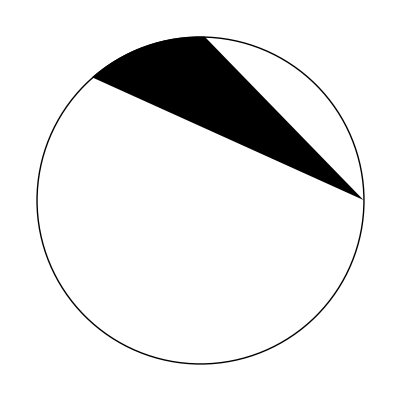

```mathematica
aL=-3.95527;
aR=1.54252;
aR=aR-2π;
x=Table[{N[Cos[i]], N[Sin[i]]}, {i,aR,aL,0.05}]
Graphics[{
Polygon[Append[Table[{N[Cos[i]], N[Sin[i]]}, {i,aR,aL,0.05}],{1,0}]],
Circle[]}
]

(*Graphics[
Polygon[x]
]*)
```

{{-0.647,0.76249},{-0.6843,0.7292},{-0.71989,0.694088},{-0.75368,0.657241},{-0.785587,0.618752},{-0.81553,0.578715},{-0.843434,0.537233},{-0.86923,0.494407},{-0.892854,0.450346},{-0.914246,0.405159}}

{{0.957826,0.287348},{0.970991,0.239118},{0.981728,0.190289},{0.990012,0.140986},{0.995821,0.0913296},{0.999141,0.0414451}}

{{-0.647,0.76249},{-0.6843,0.7292},{-0.71989,0.694088},{-0.75368,0.657241},{-0.785587,0.618752},{-0.81553,0.578715},{-0.843434,0.537233},{-0.86923,0.494407},{-0.892854,0.450346},{-0.914246,0.405159},{{0.957826,0.287348},{0.970991,0.239118},{0.981728,0.190289},{0.990012,0.140986},{0.995821,0.0913296},{0.999141,0.0414451}}}

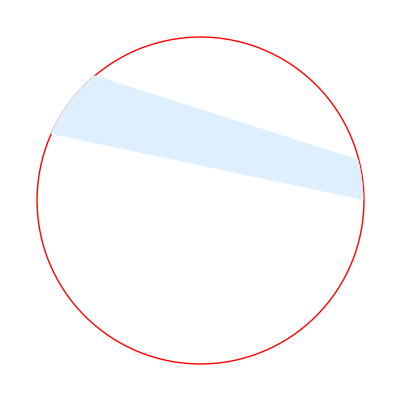

```mathematica
lHAng=-3.52094;
rHAng=2.27444;
ptLAng=0.0000;
ptRAng=0.291457;
lTable=Table[{N[Cos[i]], N[Sin[i]]}, {i,rHAng-2π,lHAng,0.05}]
rTable=Table[{N[Cos[i]], N[Sin[i]]}, {i,ptRAng,ptLAng,-0.05}]
totalTable=Append[lTable,rTable]
Graphics[{
{Red,Circle[]},
{LightBlue,Polygon[Join[Table[{N[Cos[i]], N[Sin[i]]}, {i,rHAng-2π,lHAng,0.05}],Table[{N[Cos[i]], N[Sin[i]]}, {i,ptLAng,ptRAng,0.05}]]]}
}]
```